DISPERSION ANALYSIS OF AN ILL-POSED TWO-EQUATION MODEL

```mathematica
(* W. D. Fullmer *)
(* 1/2016 *)
```

```mathematica
A = {{1, 0},{ 0,1}}
```

{{1,0},{0,1}}

```mathematica
B = {{u0, -c},{1+v0/2,u0}}
```

{{u0,-c},{1+v0/2,u0}}

```mathematica
G={{-μ,0},{0,-μ}}
```

{{-μ,0},{0,-μ}}

```mathematica
F={{b, 0},{0,b}}
```

{{b,0},{0,b}}

```mathematica
VN={{(1-g)/Δt+(u0 I/Δx)Sin[k Δx]-(2 μ/Δx^2)(Cos[k Δx]-1)+b,(-c I/Δx)Sin[k Δx]},{((1+v0/2)I/Δx)Sin[k Δx],(1-g)/Δt+(u0 I/Δx)Sin[k Δx]-(2μ/Δx^2)(Cos[k Δx]-1)+b}};
```

```mathematica
MatrixForm[A]
```

(1 | 0
0 | 1)

```mathematica
MatrixForm[B]
```

(u0 | -c
1+v0/2 | u0)

```mathematica
MatrixForm[G]
```

(-μ | 0
0 | -μ)

```mathematica
MatrixForm[F]
```

(b | 0
0 | b)

```mathematica
MatrixForm[VN]
```

(b+(1-g)/Δt-(2 μ (-1+Cos[k Δx]))/Δx^2+(ⅈ u0 Sin[k Δx])/Δx | -(ⅈ c Sin[k Δx])/Δx
(ⅈ (1+v0/2) Sin[k Δx])/Δx | b+(1-g)/Δt-(2 μ (-1+Cos[k Δx]))/Δx^2+(ⅈ u0 Sin[k Δx])/Δx)

CHARACTERISTICS

```mathematica
chareq=Det[B-s A];
```

```mathematica
charsol=Simplify[Solve[chareq==0,s]]
```

{{s→u0-(√(-c (2+v0)))/(√2)},{s→u0+(√(-c (2+v0)))/(√2)}}

DISPERSION

```mathematica
dispeq=Det[(-I ω)A+(I k)B+(I k)^2 G+F];
```

```mathematica
soln=FullSimplify[Solve[dispeq==0,ω]]
```

{{ω→k u0-(√(-c k^2 (2+v0)))/(√2)-ⅈ (b+k^2 μ)},{ω→k u0+(√(-c k^2 (2+v0)))/(√2)-ⅈ (b+k^2 μ)}}

von Neumann

```mathematica
Δsoln=FullSimplify[Solve[Det[VN]==0,g]]
```

{{g→1+b Δt-(2 Δt μ (-1+Cos[k Δx]))/Δx^2+(ⅈ u0 Δt Sin[k Δx])/Δx-(Δt √(c (2+v0) Sin[k Δx]^2))/(√2 Δx)},{g→1+b Δt-(2 Δt μ (-1+Cos[k Δx]))/Δx^2+(ⅈ u0 Δt Sin[k Δx])/Δx+(Δt √(c (2+v0) Sin[k Δx]^2))/(√2 Δx)}}

Homogeneous State

```mathematica
u0=0;v0=0;
soln0=FullSimplify[Solve[dispeq==0,ω]]
```

{{ω→-ⅈ (b+k (-√c+k μ))},{ω→-ⅈ (b+k (√c+k μ))}}

```mathematica
Δsoln0=FullSimplify[Solve[Det[VN]==0,g]]
```

{{g→(Δx^2+b Δt Δx^2+2 Δt μ-2 Δt μ Cos[k Δx]-√c Δt Δx Sin[k Δx])/Δx^2},{g→(Δx^2+b Δt Δx^2+2 Δt μ-2 Δt μ Cos[k Δx]+√c Δt Δx Sin[k Δx])/Δx^2}}

```mathematica
(*Growth Rate*)
```

```mathematica
ωIp=-b+Sqrt[c]k-μ k^2;
```

```mathematica
(*Critical Wavenumber*)
```

```mathematica
FullSimplify[Solve[D[ωIp,k]==0,k]]
```

{{k→(√c)/(2 μ)}}

```mathematica
kc=Sqrt[c]/(2μ);
```

```mathematica
(*Critical Growth Rate*)
```

```mathematica
k=kc;ωIpc=FullSimplify[ωIp]
```

-b+c/(4 μ)

```mathematica
Clear[k];
```

```mathematica
(*Cutoff wavenumber*)
```

```mathematica
k0=FullSimplify[Solve[ωIp==0,k]]
```

{{k→(√c-√(c-4 b μ))/(2 μ)},{k→(√c+√(c-4 b μ))/(2 μ)}}

```mathematica
(*Critical-Cutoff-coincident Wavenumber*)
```

```mathematica
kT=Sqrt[c0]/(2μ);
```

```mathematica
(*Cutoff c*)
```

```mathematica
cT=4 b μ;
```

```mathematica
FullSimplify[kT]
```

(√c0)/(2 μ)

```mathematica
(*Setting Params: kT==2 -> b=4μ *)
```

```mathematica
μ=0.05;
b=16μ;
```

```mathematica
(*Plot*)
```

```mathematica
cT
```

0.16

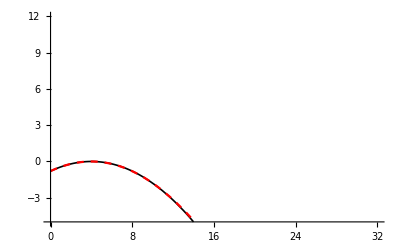

```mathematica
Clear[k];
c=0.16;
Δt=0.01;
Δx=2 Pi/256;fig1a=Plot[{Max[Im[ω/.soln0[[1]]],Im[ω/.soln0[[2]]]],Min[Log[g/.Δsoln0[[1]]],Log[g/.Δsoln0[[2]]]]/-Δt},{k,0,Pi/Δx},PlotStyle->{{Black,Thickness[0.003]},{Red,Dashed,Thickness[0.004]}},PlotRange->{{0,2Pi/(8Δx)},{-5,12}},AxesOrigin->{0,-5}]
```

```mathematica
(* value of c for ωIpc=10 10=c/4μ - b*)
```

```mathematica
(10+b)4μ
```

2.16

```mathematica
(2.16-0.16)/.16
```

12.5

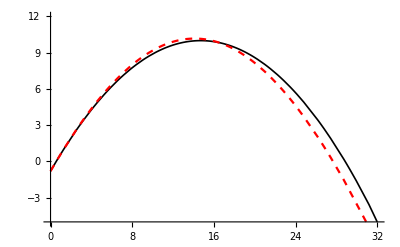

```mathematica
Clear[k];
c=2.16;
Δt=0.01;
Δx=2 Pi/256;fig1c=Plot[{Max[Im[ω/.soln0[[1]]],Im[ω/.soln0[[2]]]],Min[Log[g/.Δsoln0[[1]]],Log[g/.Δsoln0[[2]]]]/-Δt},{k,0,Pi/Δx},PlotStyle->{{Black,Thickness[0.003]},{Red,Dashed,Thickness[0.004]}},PlotRange->{{0,2Pi/(8Δx)},{-5,12}},AxesOrigin->{0,-5}]
```

```mathematica
2Pi/(2Δx)
```

128

```mathematica
2Pi/(8Δx)
```

32

```mathematica
k0
```

{{k→0.554803},{k→28.8391}}

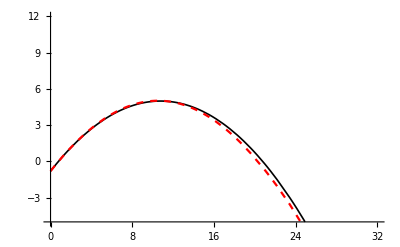

```mathematica
Clear[k];
c=1.16;
Δt=0.01;
Δx=2 Pi/256;fig1b=Plot[{Max[Im[ω/.soln0[[1]]],Im[ω/.soln0[[2]]]],Min[Log[g/.Δsoln0[[1]]],Log[g/.Δsoln0[[2]]]]/-Δt},{k,0,Pi/Δx},PlotStyle->{{Black,Thickness[0.003]},{Red,Dashed,Thickness[0.004]}},PlotRange->{{0,2Pi/(8Δx)},{-5,12}},AxesOrigin->{0,-5}]
```

```mathematica
(* plot a zero line *)
```

```mathematica
fig10=Plot[{0},{k,0,Pi/Δx},PlotStyle->{{Black,Thickness[0.001]}},PlotRange->{{0,2Pi/(8Δx)},{-5,12}},AxesOrigin->{0,-5}];
```

```mathematica
(* plot ωc = c/4μ - b vs k -> need to set k = kc = Sqrt[c]/(2μ) or, re-arranging, c = (2 k μ)^2, therefore ωc = (2kμ)^2/4μ - b = μk^2 - b *)
```

```mathematica
fig1ωc=Plot[{μ k^2-b},{k,0,Pi/Δx},PlotStyle->{{Black,Dotted,Thickness[0.001]}},PlotRange->{{0,2Pi/(8Δx)},{-5,12}},AxesOrigin->{0,-5}];
```

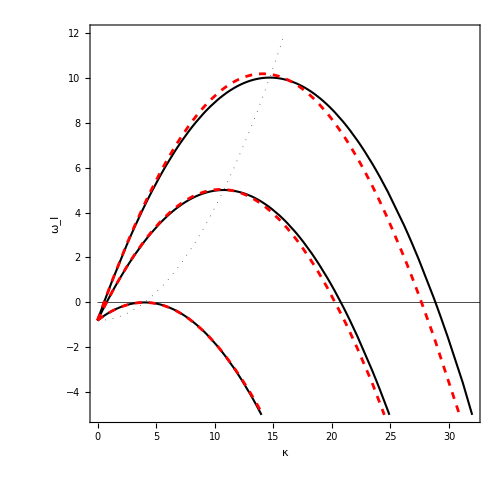

```mathematica
Show[fig10,fig1ωc,fig1c,fig1b,fig1a,Frame->True,AspectRatio->1,FrameLabel->{"κ","ω_I"},BaseStyle->{FontSize->18,FontWeight->Plain,FontFamily->Times},ImageSize->500]
```

```mathematica
(*,ImageResolution->300*)
Export["/home/curie/b/wfullmer/K&Y_Linear_Stability_Fig.eps",%37,"EPS"]
```